# Simple illustration for using Genetic Algorithms for extremizing a function

## Hyperparameters

```mathematica
maxGens=2;
populationSize=50;
mutationRate=0.1;
```

## Function to extremize

```mathematica
f[x_,y_]:=x^2+y^2+6Sin[2x]+6Sin[2y]
```

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

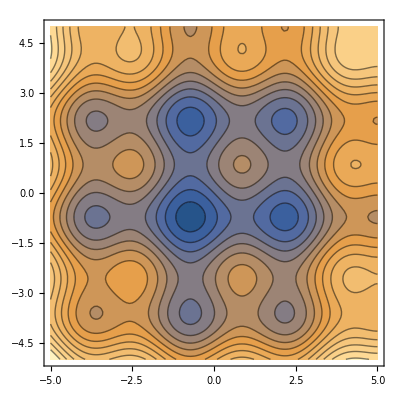

```mathematica
pot=ContourPlot[f[x,y],{x,-5,5},{y,-5,5},Contours->15]
```

## Randomly initialize first generation

```mathematica
populations={RandomReal[{-4.5,4.5},{populationSize,2}]};
```

```mathematica
pop=ListPlot[populations[[1]],PlotStyle->{Directive[Red,PointSize[0.03]]}];
```

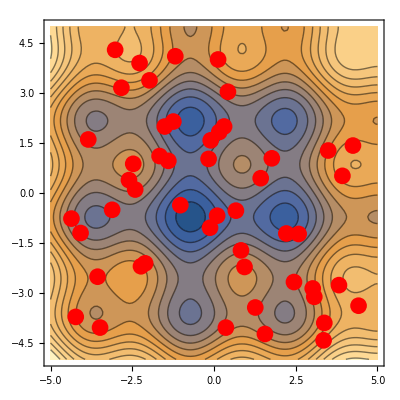

```mathematica
Show[pot,pop]
```

## Run over several generations

```mathematica
For[gen=1,gen≤maxGens,gen++,
population={};
(* Evaluate by fitness *)
fitness=Table[-(f@@populations[[-1,i]])-> populations[[-1,i]],{i,Length[populations[[-1]]]}];

(* Reproduction by tournament selection *)
children={};
For[i=1,i≤ 2 populationSize,i++,
(* 1. play 2 binary tournaments with repetition to find the two parents *)
rSamp=RandomInteger[{1,Length[fitness]},4];
candidates=Table[fitness[[i]],{i,rSamp}];
p1=Sort[{candidates[[1]],candidates[[2]]}][[-1,2]];
p2=Sort[{candidates[[3]],candidates[[4]]}][[-1,2]];
r=RandomReal[];
(*get two children*)
chromosomeC1={(r p1[[1]]+(1-r)p2[[1]]),(r p1[[2]]+(1-r)p2[[2]])};
chromosomeC2={(r p2[[1]]+(1-r)p1[[1]]),(r p2[[2]]+(1-r)p1[[2]])};
AppendTo[children,-(f@@chromosomeC1)->chromosomeC1];
AppendTo[children,-(f@@chromosomeC2)->chromosomeC1];
];

(* Survival by tournament selection *)
population={};
For[i=1,i≤ populationSize,i++,
(* 1. play a 6-way tournament with repetition to find the winning individual *)
rSamp=RandomInteger[{1,Length[children]},6];
survivor=Sort[Table[children[[i]],{i,rSamp}]][[-1]];
AppendTo[population,survivor[[2]]];
];

(* Mutation *)
For[i=1,i≤ populationSize,i++,
(*mutate first allele*)
If[RandomReal[]<mutationRate,
population[[i,1]]+=RandomVariate[NormalDistribution[0,0.5]];
];
If[RandomReal[]<mutationRate,
population[[i,2]]+=RandomVariate[NormalDistribution[0,0.5]];
];
];

AppendTo[populations,population];
];
```

## Show the results

1. Generation

```mathematica
Show[pot,ListPlot[populations[[1]],PlotStyle->{Directive[Red,PointSize[0.03]]}]]
```

-Graphics-

2. Generation

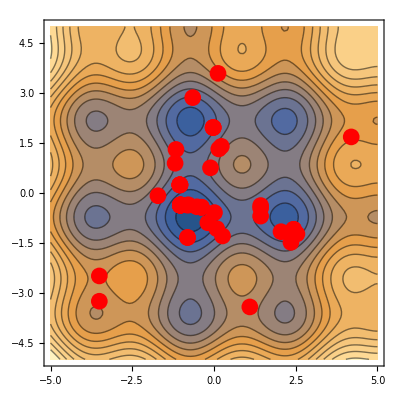

```mathematica
Show[pot,ListPlot[populations[[2]],PlotStyle->{Directive[Red,PointSize[0.03]]}]]
```

3. Generation

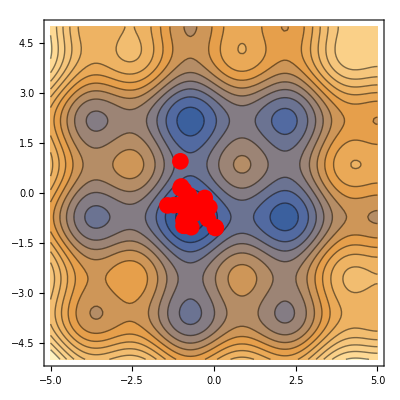

```mathematica
Show[pot,ListPlot[populations[[3]],PlotStyle->{Directive[Red,PointSize[0.03]]}]]
```